## Import astro

InterpolatingFunction[…]

2.62585×10^-10

0.

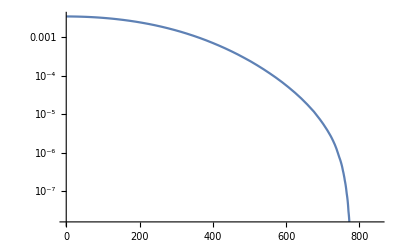

```mathematica
SetDirectory[NotebookDirectory[]];
Lgvmin=Import["gvmin_round.dat"];
ResetDirectory[];
fgvmin=Interpolation[Lgvmin,InterpolationOrder->1]
fgvmin[779]
fgvmin[780]

LogPlot[fgvmin[vmin],{vmin,0,850}]
```

## Import fion

InterpolatingFunction[…]

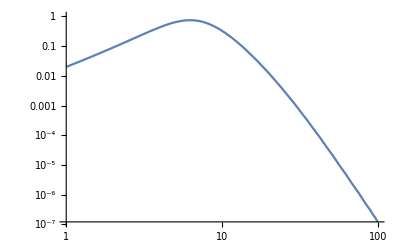

```mathematica
(*set path to form factor files*)
SetDirectory[NotebookDirectory[]<>"../Formfactor_HX"];
(*set path to form factor files*)

L1s=Import["He1s_Sch_grid.dat"];
ResetDirectory[];

f1s=Interpolation[L1s,InterpolationOrder->1]

LogLogPlot[{f1s[qx,0.02]},{qx,1,100}]
```

## Parameters

```mathematica
Params1s=Association[
wnl->2,
Inl->24.6,
fionnl->f1s
];
```

## Rate calculation: FDM = 1

σe40 is the cross section relative to 10^-40 cm^2

#### dR/dE calculation: FDM = 1

```mathematica
TdRdE[mDMMeV0_,MNGeV0_,σe40_,Params0_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40,Params1=Params0},

wnl1=Params1[wnl];
IeV1=Params1[Inl];
fion1=Params1[fionnl];

ρ=0.3;(*GeV cm^-3*)
σe=10^-40 σe40a;(*cm^2*)
convert=4.355983 10^44;(*to convert from cm^-1 keV MeV^-3 km^-1 s to kg^-1 keV^-1 day^-1*)

meMeV=.510998928;(*MeV*)
μeMeV[mDM_]:=mDM meMeV /(meMeV +mDM);(*MeV*)

vmax=779;
ke[Eex0_]:=(2. meMeV Eex0)^0.5; (*returns momentum in keV (me MeV, Ee in eV)*)
KEmaxkeV[mDM0MeV_]:=0.5 mDM0MeV 10^3(vmax/(3 10^5))^2;
vmin[mDM0MeV_,Ee0eV_,q0keV_,I0eV_]:=Abs[(  q0keV/(2. mDM0MeV ) +(I0eV+Ee0eV)/q0keV  ) 300.];

qmaxkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1+Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];
qminkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1-Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];

dRdEdq[mdmMeV_,qkeV_,EekeV_,IeV_,wnl_,fion_]:=  ρ/(MNGeV mdmMeV)wnl convert 1/EekeV  σe/(8 μeMeV[mdmMeV]^2)  qkeV fgvmin[vmin[mdmMeV,10^3 EekeV,qkeV,IeV]]fion[qkeV,EekeV];

EikeV=0.001;
EfkeV=1.0;
steps=150;

TdRdE1[mdmMeV_,IeV_,wnl_,fion_]:=Table[{10.^log10EkeV,
 NIntegrate[dRdEdq[mdmMeV,qx,10^log10EkeV,IeV,wnl,fion],{qx,qminkeV[mdmMeV,10^log10EkeV,IeV/1000.],qmaxkeV[mdmMeV,10^log10EkeV,IeV/1000.]},Method->{Automatic,"SymbolicProcessing"->False}]},{log10EkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

TRoutput=TdRdE1[mDMMeV,IeV1 ,wnl1,fion1]

]
```

#### dR/dE total calculation: FDM=1

```mathematica
TdRETotal[mDMMeV0_,MNGeV0_,σe40_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40},

fσ1s=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params1s],InterpolationOrder->1];

Ftot[x_]:=fσ1s[x];

EikeV=0.001;
EfkeV=1.0;
steps=250;

Ttotal=Table[{10^log10ErkeV,Ftot[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}]
]
```

### Calculate and Plot

```mathematica
AHe=4.0023;
MNGeV=AHe .931494; (*GeV*)
σ1=1; (*10^-40cm^2 cross section*)

TR30MeV=TdRETotal[30,MNGeV,σ1];
TR300MeV=TdRETotal[300,MNGeV,σ1];
TR1000MeV=TdRETotal[1000,MNGeV,σ1];

SetDirectory[NotebookDirectory[]];
Export["dRdE_He_30MeV.dat",TR30MeV]
Export["dRdE_He_300MeV.dat",TR300MeV]
Export["dRdE_He_1000MeV.dat",TR1000MeV]
ResetDirectory[];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {19.7791}. NIntegrate obtained 5.07502 and 0.0000991511 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {21.1117}. NIntegrate obtained 5.03075 and 0.000115607 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {22.4443}. NIntegrate obtained 4.98511 and 0.000104062 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {17.3633054316211}. NIntegrate obtained 1.31271 and 0.000738241 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {20.5379}. NIntegrate obtained 1.30357 and 0.00112891 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {20.5976}. NIntegrate obtained 1.29528 and 0.000561553 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {18.92156621601849764147118548862636089324951171875}. NIntegrate obtained 0.418142 and 0.000431863 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {45.6324}. NIntegrate obtained 0.414734 and 0.000213165 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {18.958732593693770951404076186008751392364501953125}. NIntegrate obtained 0.41263 and 0.000422228 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

dRdE_He_30MeV.dat

dRdE_He_300MeV.dat

dRdE_He_1000MeV.dat

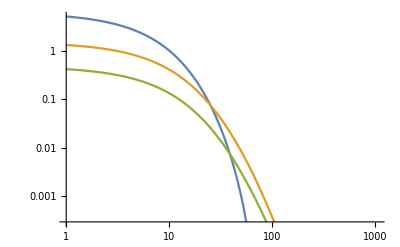

```mathematica
(*convert x-axis to eV*)
TR30MeV[[All,1]]=10^3 TR30MeV[[All,1]];
TR300MeV[[All,1]]=10^3 TR300MeV[[All,1]];
TR1000MeV[[All,1]]=10^3 TR1000MeV[[All,1]];


Show[ListLogLogPlot[{TR30MeV,TR300MeV,TR1000MeV},Joined->True,PlotRange->{{1,1070},{3 10^-4,Automatic}}]]
```

## Rate calculation: FDM = (alpha me / q)^2

σe35 is the cross section relative to 10^-37 cm^2

#### dR/dE calculation: FDM = (alpha me / q)^2

```mathematica
TdRdElightmed[mDMMeV0_,MNGeV0_,σe37_,Params0_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37,Params1=Params0},

wnl1=Params1[wnl];
IeV1=Params1[Inl];
fion1=Params1[fionnl];

αEM=1/137.04;
ρ=0.3;(*GeV cm^-3*)
σe=10^-37 σe37a;(*cm^2*)
convert=4.355983 10^44;(*to convert from cm^-1 keV MeV^-3 km^-1 s to kg^-1 keV^-1 day^-1*)

meMeV=.510998928;(*MeV*)
mekeV=1000. meMeV;(*keV*)
μeMeV[mDM_]:=mDM meMeV /(meMeV +mDM);(*MeV*)

vmax=779;
ke[Eex0_]:=(2. meMeV Eex0)^0.5; (*returns momentum in keV (me MeV, Ee in eV)*)
KEmaxkeV[mDM0MeV_]:=0.5 mDM0MeV 10^3(vmax/(3 10^5))^2;
vmin[mDM0MeV_,Ee0eV_,q0keV_,I0eV_]:=Abs[(  q0keV/(2. mDM0MeV ) +(I0eV+Ee0eV)/q0keV  ) 300.];

qmaxkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1+Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];
qminkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1-Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];

FDM[qkeV_]:=(αEM mekeV/qkeV)^2;

dRdEdq[mdmMeV_,qkeV_,EekeV_,IeV_,wnl_,fion_]:=   FDM[qkeV]^2ρ/(MNGeV mdmMeV)wnl convert 1/EekeV  σe/(8 μeMeV[mdmMeV]^2)  qkeV fgvmin[vmin[mdmMeV,10^3 EekeV,qkeV,IeV]]fion[qkeV,EekeV];

EikeV=0.001;
EfkeV=1.0;
steps=150;

TdRdE1[mdmMeV_,IeV_,wnl_,fion_]:=Table[{10.^log10EkeV,
 NIntegrate[dRdEdq[mdmMeV,qx,10^log10EkeV,IeV,wnl,fion],{qx,qminkeV[mdmMeV,10^log10EkeV,IeV/1000.],qmaxkeV[mdmMeV,10^log10EkeV,IeV/1000.]},Method->{Automatic,"SymbolicProcessing"->False}]},{log10EkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

TRoutput=TdRdE1[mDMMeV,IeV1 ,wnl1,fion1]

]
```

#### dR/dE total calculation: FDM = (alpha me / q)^2

```mathematica
TdRETotallightmed[mDMMeV0_,MNGeV0_,σe37_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37},

fσ1s=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params1s],InterpolationOrder->1];

Ftot[x_]:=fσ1s[x];

EikeV=0.001;
EfkeV=1.0;
steps=250;

Ttotal=Table[{10^log10ErkeV,Ftot[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}]
]
```

### Calculate and Plot

```mathematica
AHe=4.0023;
MNGeV=AHe .931494; (*GeV*)
σ1=1; (*10^-37cm^2 cross section*)

TR30MeVlightmed=TdRETotallightmed[30,MNGeV,σ1];
TR300MeVlightmed=TdRETotallightmed[300,MNGeV,σ1];
TR1000MeVlightmed=TdRETotallightmed[1000,MNGeV,σ1];

SetDirectory[NotebookDirectory[]];
Export["dRdE_He_30MeV_lightmed.dat",TR30MeVlightmed]
Export["dRdE_He_300MeV_lightmed.dat",TR300MeVlightmed]
Export["dRdE_He_1000MeV_lightmed.dat",TR1000MeVlightmed]
ResetDirectory[];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {19.7791}. NIntegrate obtained 8.06504 and 0.000126488 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {21.1117}. NIntegrate obtained 7.94756 and 0.000150568 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {19.8162}. NIntegrate obtained 7.82673 and 0.000099067 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {17.36330543162105488619317839038558304309844970703125}. NIntegrate obtained 2.20874 and 0.00113289 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {17.38151155856850049730155660654418170452117919921875}. NIntegrate obtained 2.18153 and 0.00174839 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {17.40057618031450825668571269488893449306488037109375}. NIntegrate obtained 2.15626 and 0.00161589 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {14.0613546218757203831728475051932036876678466796875}. NIntegrate obtained 0.710018 and 0.000424077 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {25.8664}. NIntegrate obtained 0.701334 and 0.000535884 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {18.958732593693770951404076186008751392364501953125}. NIntegrate obtained 0.693117 and 0.000899209 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dRdE_He_30MeV_lightmed.dat

dRdE_He_300MeV_lightmed.dat

dRdE_He_1000MeV_lightmed.dat

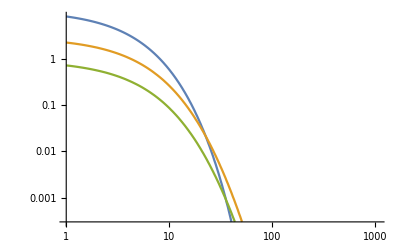

```mathematica
(*convert x-axis to eV*)
TR30MeVlightmed[[All,1]]=10^3 TR30MeVlightmed[[All,1]];
TR300MeVlightmed[[All,1]]=10^3 TR300MeVlightmed[[All,1]];
TR1000MeVlightmed[[All,1]]=10^3 TR1000MeVlightmed[[All,1]];


Show[ListLogLogPlot[{TR30MeVlightmed,TR300MeVlightmed,TR1000MeVlightmed},Joined->True,PlotRange->{{1,1070},{3 10^-4,Automatic}}]]
```